# Pruebas de gráficas y recolección de datos de experimentos

## Conexión con Netlogo :

Hay que editar los valores de $NLHome (carpeta del ejecutable de netlogo) y $NLModel (carpeta donde está) con los de la máquina local.

```mathematica
<<NetLogo`
$NLHome= "/opt/netlogo-4.0.5";
$NLModel="/home/erikasv/github/Collective-intelligence--Analysis-and-modeling";
NLStart[];
NLCommand["no-display"];
NLLoadModel[ToFileName[{$NLModel},"modelo.nlogo"]];
```

## Definición de experimentos

### ExpPeopleSize: Ajuste de parámetros: people, selection-size y unidades de tiempo (por configuración)

```mathematica
ExpPeopleSize[p_,s_,n_]:=Module[{},
NLCommand["set num-people ",p, "set selection-size ",s,"setup"];
Mean[NLDoReport["go","clustering-coefficient",n]]
];
```

### ExpPeopleProperties: Ajuste de parámetros: people, properties-proportion y unidades de tiempo (por configuración)

```mathematica
ExpPeopleProperties[p_,pr_,n_]:=Module[{},
NLCommand["set num-people ",p, "set properties-proportion ",pr,"setup"];
Mean[NLDoReport["go","clustering-coefficient",n]]
];
```

## Recolección de datos:

### ExpPeopleSize

```mathematica
people=Table[{i,j,2},{i,10,100,10},{j,1,100,20}];
NLCommand["no-display"];
clusteringData=Table[{Apply[ExpPeopleSize,Flatten[people,1][[i]]]},{i,1,Length[Flatten[people,1]]}];
```

### ExpPeopleProperties

```mathematica
people=Table[{i,j,2},{i,10,100,10},{j,1,100,20}];
NLCommand["no-display"];
clusteringData2=Table[{Apply[ExpPeopleProperties,Flatten[people,1][[i]]]},{i,1,Length[Flatten[people,1]]}];
```

## Gráficas :

### ExpPeopleSize

```mathematica
xy=Table[{i,j},{i,10,100,10},{j,1,100,20}];
dataPlot=Table[Join[Flatten[xy,1][[c]],clusteringData[[c]]],{c,1,50,1}];
```

```mathematica
ListPlot3D[dataPlot,ColorFunction->"SouthwestColors"]
```

-Graphics3D-

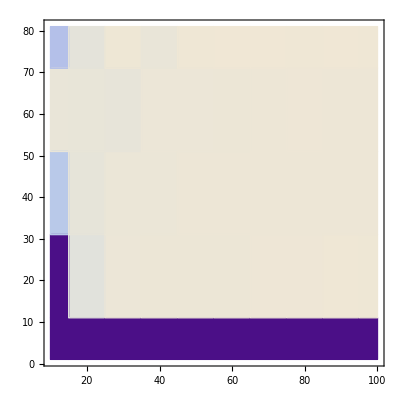

```mathematica
ListDensityPlot[dataPlot,VertexColors->{Red,Green,Yellow,Blue}, Mesh->None,InterpolationOrder->0,PlotRange->All, BoundaryStyle->Red]
```

### ExpPeopleProperties

```mathematica
xy=Table[{i,j},{i,10,100,10},{j,1,100,20}];dataPlot2=Table[Join[Flatten[xy,1][[c]],clusteringData2[[c]]],{c,1,50,1}];
```

```mathematica
ListPlot3D[dataPlot2,ColorFunction->"SouthwestColors"]
```

-Graphics3D-

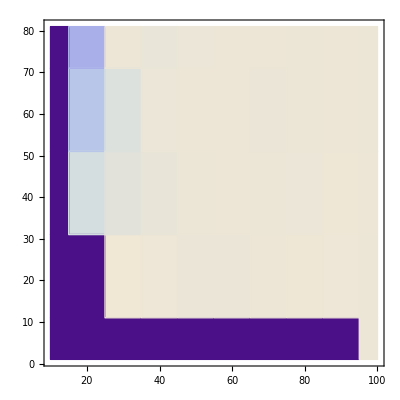

```mathematica
ListDensityPlot[dataPlot2,VertexColors->{Red,Green,Yellow,Blue}, Mesh->None,InterpolationOrder->0,PlotRange->All, BoundaryStyle->Red]
```